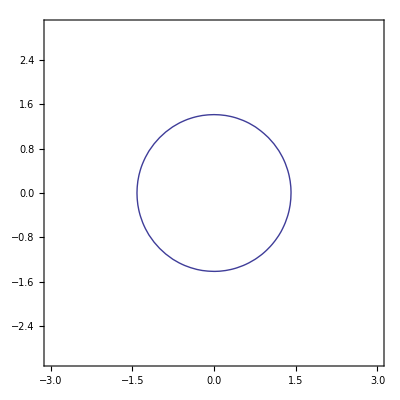

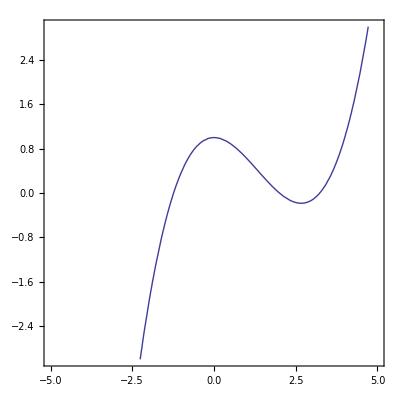

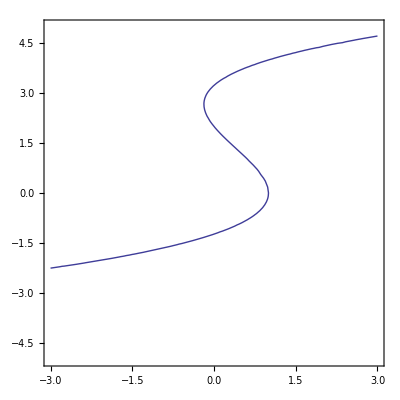

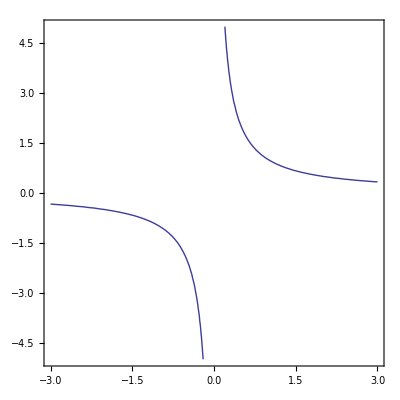

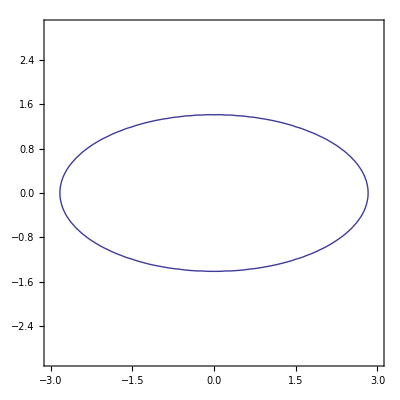

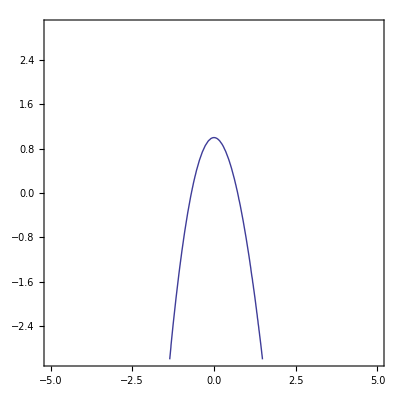

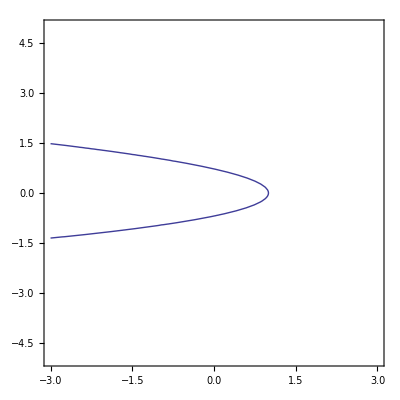

```mathematica
nonFxn1a=ContourPlot[x^2+y^2==2,{x,-3,3},{y,-3,3}]
fxn2a=ContourPlot[(x/2)^3-2(x/2)^2+1==y,{x,-5,5},{y,-3,3}]
nonFxn3a=ContourPlot[(y/2)^3-2(y/2)^2+1==x,{x,-3,3},{y,-5,5}]
fxn4=ContourPlot[x*y==1,{x,-3,3},{y,-5,5}]

nonFxn1b=ContourPlot[(x/2)^2+y^2==2,{x,-3,3},{y,-3,3}]
fxn2b=ContourPlot[(x/2)^3-2(x)^2+1==y,{x,-5,5},{y,-3,3}]
nonFxn3b=ContourPlot[(y/2)^3-2(y)^2+1==x,{x,-3,3},{y,-5,5}]
```

```mathematica
Export["nonFxn1a.png",nonFxn1a]
Export["nonFxn1b.png",nonFxn1b]
Export["fxn2a.png",fxn2a]
Export["fxn2b.png",fxn2b]
Export["nonFxn3a.png",nonFxn3a]
Export["nonFxn3b.png",nonFxn3b]
Export["fxn4.png",fxn4]
```

nonFxn1a.png

nonFxn1b.png

fxn2a.png

fxn2b.png

nonFxn3a.png

nonFxn3b.png

fxn4.png

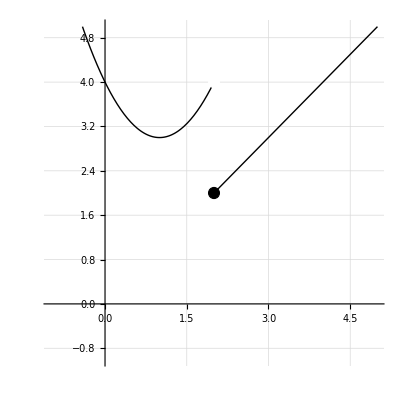

```mathematica
curve1=Plot[((x-1))^2+3, {x,-1,2},PlotStyle->{Black,Thick},PlotRange->{-1,5},GridLines->Automatic];
curve2=Plot[x, {x,2,5},PlotStyle->{Black,Thick},PlotRange->{-1,5},GridLines->Automatic];
circ=Graphics[{{EdgeForm[Thick],White,Disk[{2,4},.1]},{EdgeForm[Thick],Black,Disk[{2,2},.1]}}];
plot1Exam=Show[curve1,curve2,circ,PlotRange->{{-1,5},{-1,5}},AspectRatio->1]
```

```mathematica
Export["plot1Exam.png",plot1Exam]
```

plot1Exam.png